### Ground truth

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]];
fileName= FileNameJoin[{NotebookDirectory[],"2025-03-25_streakedBeam.h5"}];
data = readBeamFile[fileName];
```

```mathematica
rawTruth = 10^3{#x,#px/#pz}&/@data;
```

```mathematica
rawTruth =BinCounts[rawTruth,{-0.25,0.25,0.0005},{-0.25,0.25,0.0005}];
```

```mathematica
densityHistogramMod[10^6{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400,ChartLegends->Automatic,AspectRatio->Automatic]
```

-Graphics-

```mathematica
binSize = 10;
arrayData = BinCounts[10^6{#x,#y}&/@data,{-500,300,binSize},{-1500,1500,binSize}];
arrayData = GaussianFilter[arrayData,3];
arrayData = Reverse[Transpose[arrayData]];
```

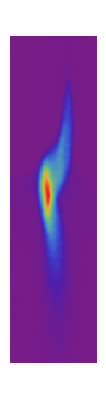

```mathematica
ArrayPlot[arrayData,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

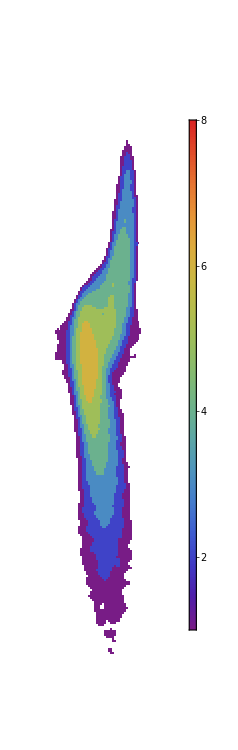

```mathematica
ArrayPlot[Floor[Log2[arrayData+0.00001]],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{1,8}},LabelStyle->20,ImageSize->200]
```

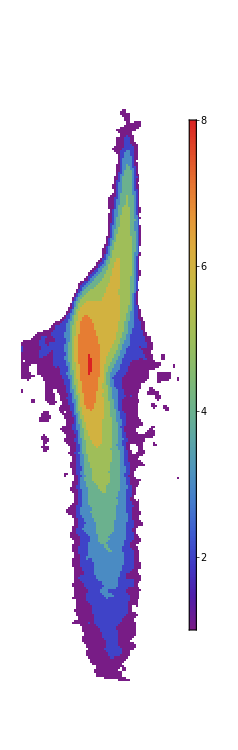

```mathematica
ArrayPlot[Floor[Log2[2.5*arrayData+0.00001]],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{1,8}},LabelStyle->20,ImageSize->200]
```

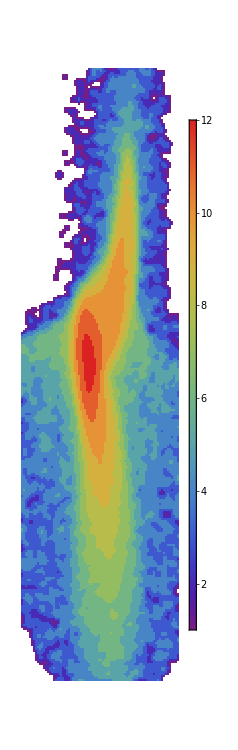

```mathematica
ArrayPlot[Floor[Log2[50*arrayData+0.00001]],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{1,12}},LabelStyle->20,ImageSize->200]
```

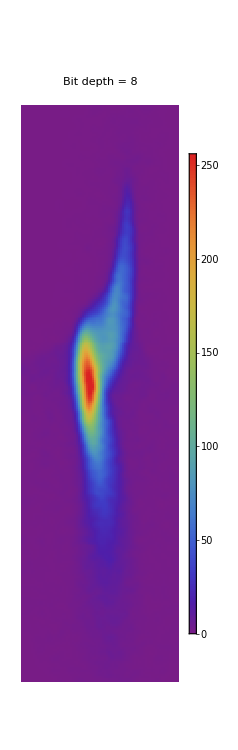
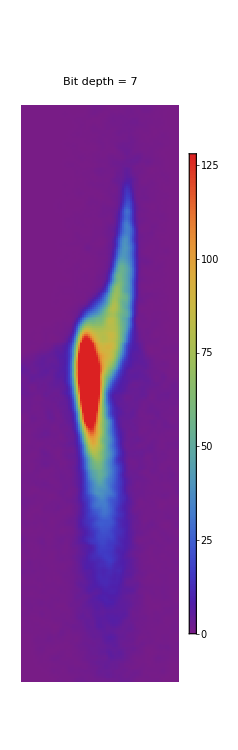
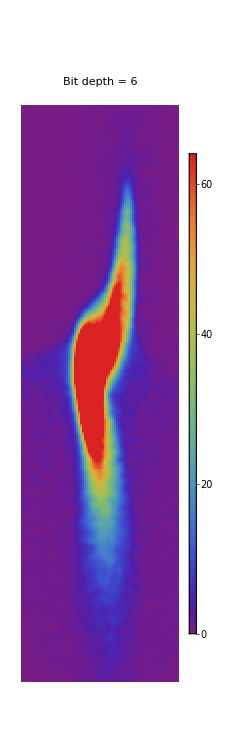
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{
ArrayPlot[Clip[2.5*arrayData+0.00001,{0,2^8}],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{0,2^8}},LabelStyle->20,ImageSize->200,PlotLabel->"Bit depth = 8"],
ArrayPlot[Clip[2.5*arrayData+0.00001,{0,2^7}],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{0,2^7}},LabelStyle->20,ImageSize->200,PlotLabel->"Bit depth = 7"],
ArrayPlot[Clip[2.5*arrayData+0.00001,{0,2^6}],ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{All,All,{0,2^6}},LabelStyle->20,ImageSize->200,PlotLabel->"Bit depth = 6"]
}}]
```